```mathematica
CreatePacletArchive["/Users/andrewyule/Dropbox (Personal)/AFS/Source Code/ggplot/ggplot","Downloads"]
PacletInstall[%,ForceVersionInstall->True]
```

/Users/andrewyule/Downloads/ggplot-0.2.paclet

PacletObject[…]

```mathematica
Quit[]
```

```mathematica
2
```

2

```mathematica
Get["Alex`"]
Get["ggplot`"]
```

Assured Flow Solutions' Alex v2020.5.3

ggplot v0.2

Get data sets

```mathematica
mpg=FileNameJoin[{NotebookDirectory[],"Data","mpg.csv"}]//importToDataset;
mtcars=FileNameJoin[{NotebookDirectory[],"Data","mtcars.csv"}]//importToDataset;
economics=FileNameJoin[{NotebookDirectory[],"Data","economics.csv"}]//importToDataset//MapAt[DateObject,{All,"date"}];
(*diamonds=FileNameJoin[{NotebookDirectory[],"Data","diamonds.csv"}]//importToDataset;*)
dates=Table[<|"date"->Now+Quantity[x,"Days"],"val"->x^2|>,{x,100}];
```

#### Faster ability to put Points in a Graphics object

GeometricTransformation can be used to take a single Inset command and replicate it at multiple locations

```mathematica
Graphics[{Red,Point[{{0,0},{1,1}}],
Blue,GeometricTransformation[Inset["A",{0,0}],{{{0.5,0.5}},{{1,1}}}]
}]
```

-Graphics-

```mathematica
GeometricTransformation[Inset[Style[■,Rule[GraphicsBoxOptions,List[Rule[DefaultBaseStyle,Directive[PointSize[0.012833333333333334],RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6]]]]]],List[0.,0.]],List[List[List[0.,0.]],List[List[1.,1.]]]]//InputForm
```

GeometricTransformation[
 Inset[Style[■, GraphicsBoxOptions -> 
    {DefaultBaseStyle -> Directive[PointSize[0.012833333333333334], 
       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]]}], {0., 0.}], 
 {{{0., 0.}}, {{1., 1.}}}]

```mathematica
GeometricTransformation
```

```mathematica
ListPlot[{{0,0},{1,1}},PlotMarkers->■]//FullForm
```

Graphics[List[List[],List[List[List[Directive[PointSize[0.0128333],RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6]],GeometricTransformation[Inset[Style[\[FilledSquare],Rule[GraphicsBoxOptions,List[Rule[DefaultBaseStyle,Directive[PointSize[0.0128333],RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6]]]]]],List[0.,0.]],List[List[List[0.,0.]],List[List[1.,1.]]]]]],List[List[Directive[PointSize[0.0128333],RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6]]],List[]],List[List[Directive[PointSize[0.0128333],RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6]]],List[]]],List[List[],List[]]],List[Rule[DisplayFunction,Identity],Rule[DisplayFunction,Identity],Rule[AspectRatio,Power[GoldenRatio,-1]],Rule[Axes,List[True,True]],Rule[AxesLabel,List[None,None]],Rule[AxesOrigin,List[0,0]],RuleDelayed[DisplayFunction,Identity],Rule[Frame,List[List[False,False],List[False,False]]],Rule[FrameLabel,List[List[None,None],List[None,None]]],Rule[FrameTicks,List[List[Automatic,Automatic],List[Automatic,Automatic]]],Rule[GridLines,List[None,None]],Rule[GridLinesStyle,Directive[GrayLevel[0.5,0.4]]],Rule[Method,List[Rule["OptimizePlotMarkers",True],Rule["CoordinatesToolOptions",List[Rule["DisplayFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]],Rule["CopiedValueFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]]]]]],Rule[PlotRange,List[List[0,1.],List[0,1.]]],Rule[PlotRangeClipping,True],Rule[PlotRangePadding,List[List[Scaled[0.02],Scaled[0.02]],List[Scaled[0.02],Scaled[0.05]]]],Rule[Ticks,List[Automatic,Automatic]]]]

#### Experimenting for aesthetics

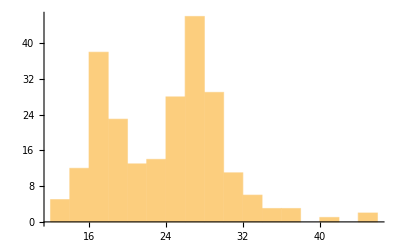

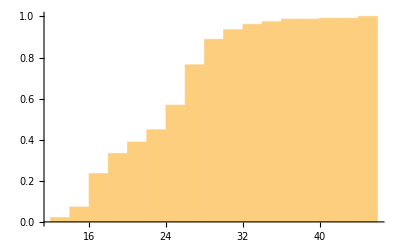

```mathematica
Histogram[mpg[[All,"hwy"]]]
Histogram[mpg[[All,"hwy"]],Automatic,"CDF"]
```

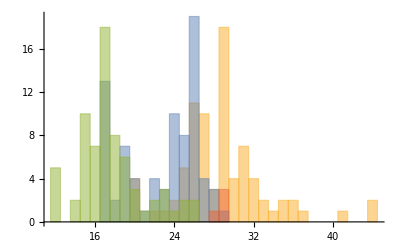

```mathematica
mpg//
	GroupBy[Function[#cyl]->Function[#hwy]]//
	op[Histogram[{1},PlotRange->All]]
```

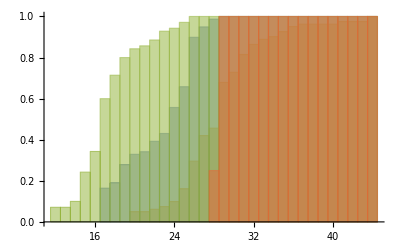

```mathematica
mpg//
	GroupBy[Function[#cyl]->Function[#hwy]]//
	op[Histogram[{1},"CDF",PlotRange->All]]
```

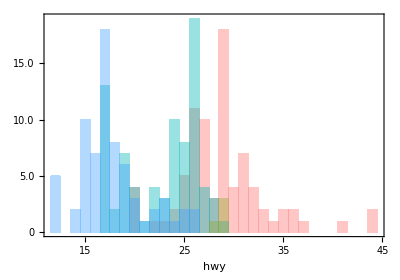

```mathematica
mpg//
	MapAt[ToString,{All,"cyl"}]//
	ggplot[geomHistogram["x"->"hwy","color"->"cyl","alpha"->Opacity[0.4],"bspec"->{1}]]
```

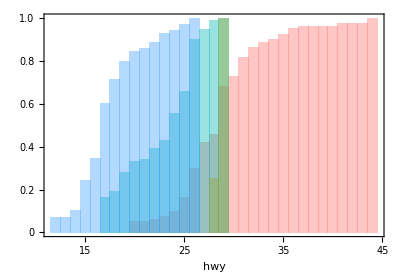

```mathematica
mpg//
	MapAt[ToString,{All,"cyl"}]//
	ggplot[geomHistogram["x"->"hwy","color"->"cyl","alpha"->Opacity[0.4],"bspec"->{1},"hspec"->"CDF"]]
```

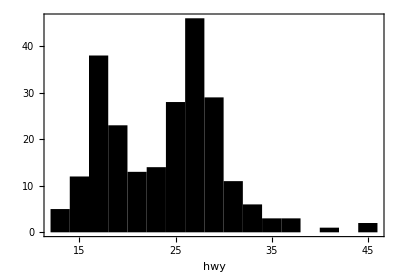

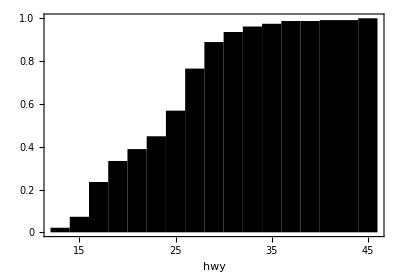

```mathematica
ggplot["data"->mpg,geomHistogram["x"->"hwy"]]
ggplot["data"->mpg,geomHistogram["x"->"hwy","hspec"->"CDF"]]
```

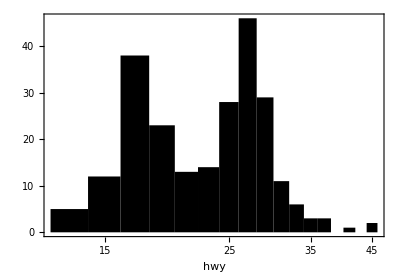

```mathematica
ggplot["data"->mpg,geomHistogram["x"->"hwy"],scaleXLog[]]
```

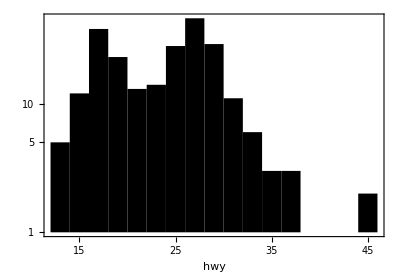

```mathematica
ggplot["data"->mpg,geomHistogram["x"->"hwy"],scaleYLog[]]
```

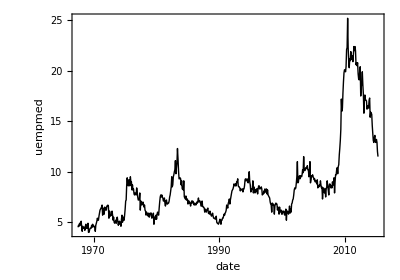

```mathematica
economics//
	ggplot[
		"x"->"date","y"->"uempmed",geomLine[],scaleXDate[]
	]
```

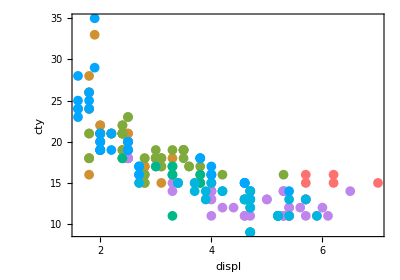

```mathematica
mpg//ggplot[geomPoint["x"->"displ","y"->"cty","color"->"class"]]
```

Need to be able to handle this kind of case

```mathematica
(*Need to be able to handle this kind of case*)
mtcars//ggplot[
	geomPoint["data"->mtcars,"x"->"disp","y"->"mpg"]
	];
```

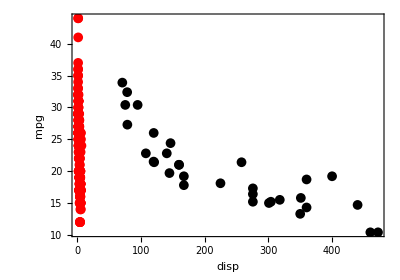

```mathematica
ggplot[mtcars,"x"->"disp","y"->"mpg",
	geomPoint[],
	geomPoint["data"->mpg,"x"->"displ","y"->"hwy","color"->Red]
]
```

```mathematica
ggplot[dates,
	geomPoint["data"->mtcars,"x"->"disp","y"->"mpg"],
	geomPoint["data"->mpg,"x"->"displ","y"->"hwy","color"->Red]
]
```

-Graphics-

```mathematica
ggplot[
geomPoint["data"->mtcars,"x"->"disp","y"->"mpg"],
geomPoint["data"->mpg,"x"->"displ","y"->"hwy","color"->Red]
]
```

-Graphics-

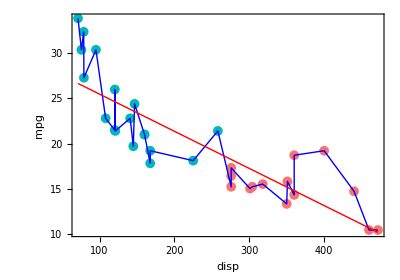

```mathematica
mtcars//
	ggplot["x"->"disp","y"->"mpg",geomPoint["color"->Function[#cyl<8]],geomLine["color"->Blue],geomSmooth["color"->Red]]
```

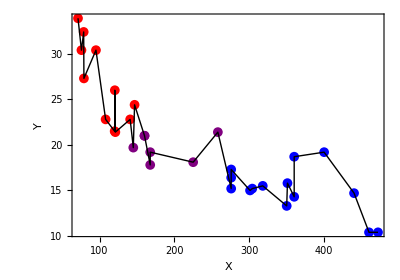

```mathematica
mtcars//
	ggplot[
		geomPoint["x"->"disp","y"->"mpg","color"->"cyl"],
		geomLine["x"->"disp","y"->"mpg","color"->Black]
	,FrameLabel->{"X","Y"}]
```

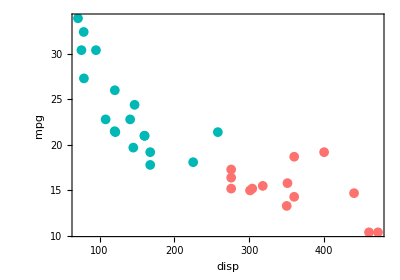

```mathematica
mtcars//ggplot[geomPoint["x"->"disp","y"->"mpg","color"->Function[#cyl<8]]]
```

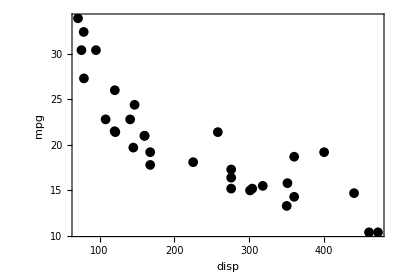

```mathematica
mtcars//ggplot[geomPoint["x"->"disp","y"->"mpg"]]
```

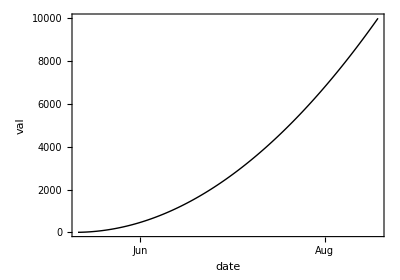

```mathematica
dates//
	ggplot[geomLine["x"->"date","y"->"val"],scaleXDate[]]
```

```mathematica
mtcars//
	ggplot["x"->"disp","y"->"mpg",geomPoint[]]
```

-Graphics-

```mathematica
ggplot["data"->mtcars,"x"->"disp","y"->"mpg",geomPoint[]]
```

-Graphics-

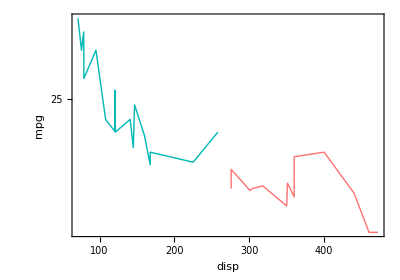

```mathematica
ggplot[
	geomLine["x"->"disp","y"->"mpg","color"->Function[#cyl<8]],
	geomParityLine["color"->Red,"alpha"->Opacity[0.2]],
	"data"->mtcars
]
```

```mathematica
ggplot["data"->mtcars,"x"->"disp","y"->"mpg",geomPoint[],geomLine[],scaleXLog[]]
```

-Graphics-

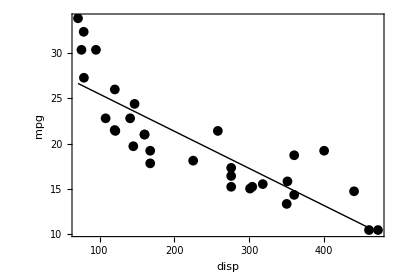

```mathematica
ggplot["data"->mtcars,"x"->"disp","y"->"mpg",geomPoint[],geomSmooth[]]
```

```mathematica
ggplot["data"->mtcars,
	geomLine["x"->"disp","y"->"mpg","color"->Function[#cyl<8]],
	geomParityLine["color"->Red,"alpha"->Opacity[0.2]]
]
```

-Graphics-

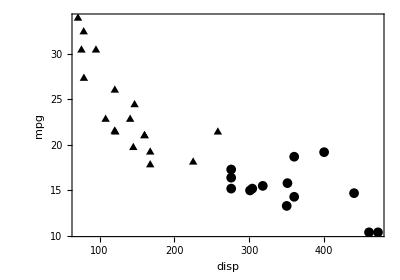

```mathematica
mtcars//
	ggplot[geomPoint["x"->"disp","y"->"mpg","shape"->(*Null*)Function[#cyl<8]]]
```

```mathematica
mtcars//
	ggplot["x"->"disp","y"->"mpg",
	geomPoint[],
	geomSmooth[],
	scaleYLog[],
	scaleXLog[]
	]
```

-Graphics-

```mathematica
ggplot[mtcars,geomPoint["x"->"disp","y"->"mpg"],geomSmooth["x"->"disp","y"->"mpg"],scaleYLog[],scaleXLog[]]
```

-Graphics-

```mathematica
ggplot[mtcars,geomPoint["x"->"disp","y"->"mpg"],geomHLine["yIntercept"->10],geomVLine["xIntercept"->100],scaleYLog[],scaleXLog[]]
```

-Graphics-

```mathematica
ggplot[mtcars,geomPoint["x"->"disp","y"->"mpg"]]
```

-Graphics-

-Graphics-

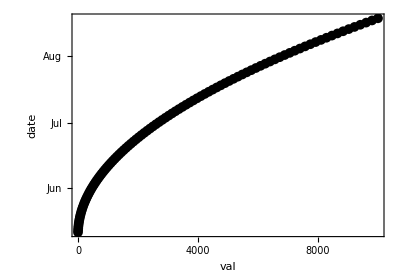

```mathematica
dates//
	ggplot[geomLine["x"->"date","y"->"val"],scaleXDate[]]
dates//
	ggplot[geomPoint["y"->"date","x"->"val"],scaleYDate[]]
```

```mathematica
mtcars//
	ggplot[geomPoint["x"->"disp","y"->"mpg"],geomSmooth["x"->"disp","y"->"mpg"]]
```

-Graphics-

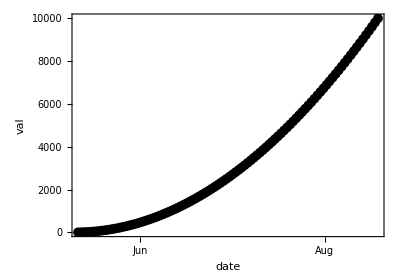

-Graphics-

```mathematica
dates//
	ggplot[geomPoint["x"->"date","y"->"val"],scaleXDate[]]
dates//
	ggplot[geomPoint["x"->"val","y"->"date"],scaleYDate[]]
```

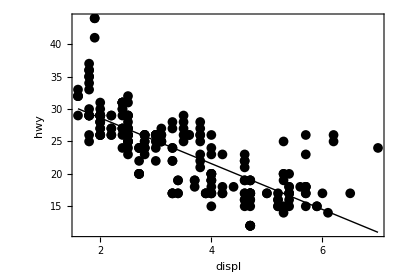

```mathematica
mpg//
	ggplot[
		geomPoint["x"->"displ","y"->"hwy"],
		geomSmooth["x"->"displ","y"->"hwy"]
	]
```

-Graphics-

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

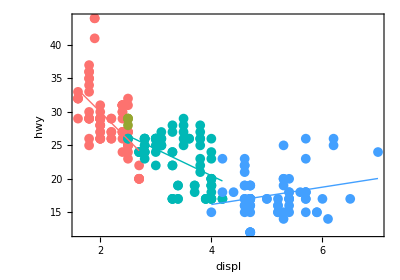

```mathematica
mpg//
	ggplot[
		geomPoint["x"->"displ","y"->"hwy"],
		geomSmooth["x"->"displ","y"->"hwy"]
	]
mpg//
	MapAt[ToString,{All,"cyl"}]//
	ggplot[
		geomPoint["x"->"displ","y"->"hwy","color"->"cyl"],
		geomSmooth["x"->"displ","y"->"hwy","color"->"cyl"]
	]
```

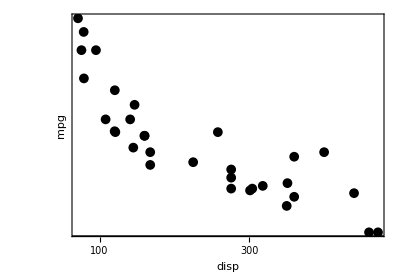

```mathematica
ggplot[mtcars,geomPoint["x"->"disp","y"->"mpg"],geomParityLine[],geomHLine["yIntercept"->10],geomVLine["xIntercept"->10,"color"->Red]]
```

```mathematica
ggplot[mtcars,geomPoint["x"->"disp","y"->"mpg"]]
(*mtcars//ggplot[geomPoint["x"->"disp","y"->"mpg"]]*)
```

-Graphics-

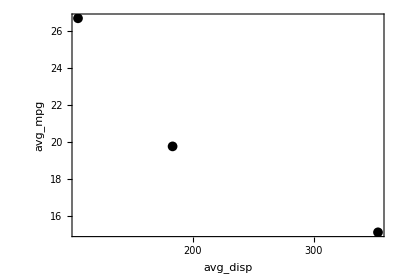

```mathematica
mtcars//
	GroupBy[#cyl&]//
	Map[summarize[{"avg_mpg"->Function[Mean@#mpg],"avg_disp"->Function[Mean@#disp]}]]//
	Values//
	ggplot[geomPoint["y"->"avg_mpg","x"->"avg_disp"]]
```

```mathematica
(*Takes a long time*)
(*diamonds//
	ggplot[geomPoint["x"->"carat","y"->"price","alpha"->Opacity[0.02]]]*)
```

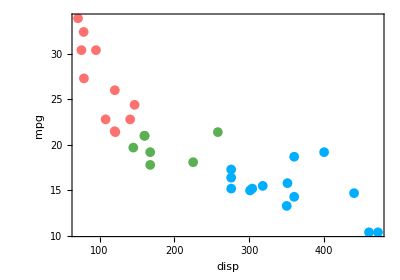

```mathematica
mtcars//
	MapAt[ToString,{{All,"cyl"},{All,"gear"}}]//
	ggplot[geomPoint["x"->"disp","y"->"mpg","color"->"cyl"]]
```

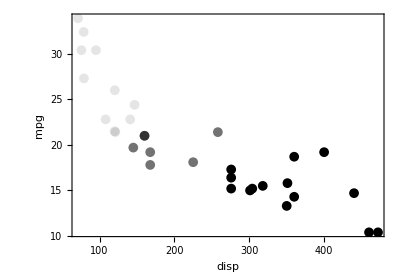

```mathematica
mtcars//
	ggplot[geomPoint["x"->"disp","y"->"mpg","alpha"->"cyl"]]
```

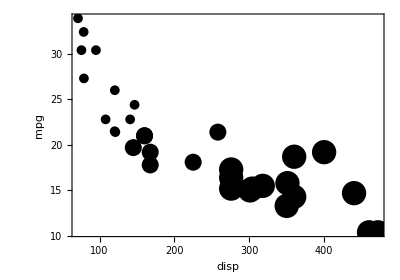

```mathematica
mtcars//
	ggplot[geomPoint["x"->"disp","y"->"mpg","size"->"cyl"]]
```

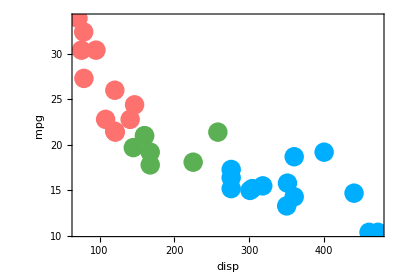

```mathematica
mtcars//
	MapAt[ToString,{All,"cyl"}]//
	ggplot[geomPoint["x"->"disp","y"->"mpg","color"->"cyl","size"->20]]
```

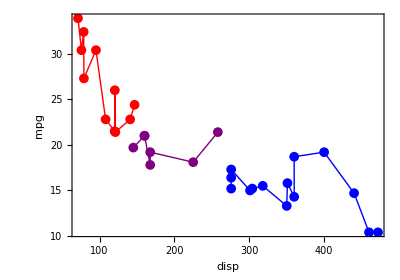

```mathematica
mtcars//
	ggplot[
		geomPoint["x"->"disp","y"->"mpg","color"->"cyl"],
		geomLine["x"->"disp","y"->"mpg","color"->"cyl"]
	]
```

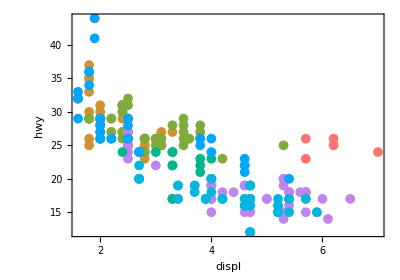

```mathematica
mpg//
	ggplot[geomPoint["x"->"displ","y"->"hwy","color"->"class"]]
```

Columns

```mathematica
(*mpg//
	ggplot[geomCol["x"->"displ","y"->"hwy"]]*)
```

#### Experimenting with coordinate and scale transforms

```mathematica
CoordinateTransform
```

```mathematica
ScalingTransform
```

```mathematica
x=RandomReal[{0,5000},{50,2}];
```

```mathematica
x
```

{{604.171,4678.13},{4528.04,4122.09},{7.12955,1352.87},{330.54,3741.},{1469.86,4414.34},{3728.29,2118.73},{175.051,1713.45},{4919.55,1013.24},{599.704,3787.8},{121.324,1792.87},{1063.68,4252.83},{4416.05,994.689},{296.035,4191.6},{4120.3,2512.06},{460.032,1519.86},{1506.73,2746.93},{1583.73,2201.3},{2324.68,2320.97},{2076.42,1904.64},{2509.8,3217.77},{4212.48,4150.62},{1968.64,1201.02},{2682.81,3814.99},{1628.31,3501.14},{4295.5,3377.52},{3408.8,962.72},{525.472,4568.01},{1717.95,4262.07},{4083.71,1932.62},{738.089,1586.93},{4502.78,1152.24},{4115.67,3221.26},{4567.6,106.174},{4590.74,4758.66},{2049.37,983.114},{2020.03,567.755},{4154.25,3938.77},{3614.72,2139.85},{4304.07,1152.22},{3728.62,1717.07},{3198.51,1552.09},{2878.99,4211.34},{1125.5,2040.74},{4199.72,3613.65},{1279.27,3942.59},{2189.7,2643.27},{3079.04,877.378},{3303.25,3211.64},{1615.54,1005.53},{352.108,3241.52}}

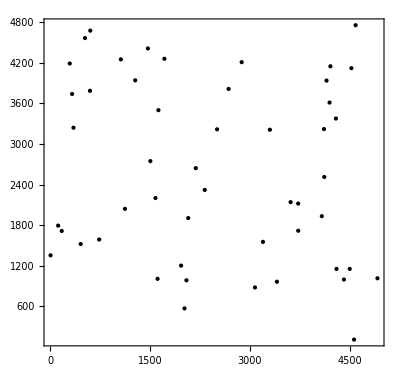

```mathematica
Graphics[Point@x,Frame->True,ScalingFunctions->"Log"]
```

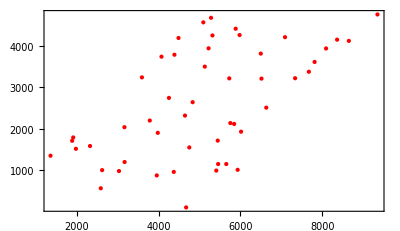

```mathematica
Graphics[GeometricTransformation[{Red,Point@x},ShearingTransform[Pi/4,{1,0},{0,1}]],Frame->True]
```

```mathematica
graphicsPrimitives=geomPoint[mtcars,"x"->"disp","y"->"mpg"]
```

{{GrayLevel[0],Opacity[1],GeometricTransformation[Inset[●,{0,0}],{{{160,21}},{{160,21}},{{108,22.8}},{{258,21.4}},{{360,18.7}},{{225,18.1}},{{360,14.3}},{{146.7,24.4}},{{140.8,22.8}},{{167.6,19.2}},{{167.6,17.8}},{{275.8,16.4}},{{275.8,17.3}},{{275.8,15.2}},{{472,10.4}},{{460,10.4}},{{440,14.7}},{{78.7,32.4}},{{75.7,30.4}},{{71.1,33.9}},{{120.1,21.5}},{{318,15.5}},{{304,15.2}},{{350,13.3}},{{400,19.2}},{{79,27.3}},{{120.3,26}},{{95.1,30.4}},{{351,15.8}},{{145,19.7}},{{301,15}},{{121,21.4}}}]}}

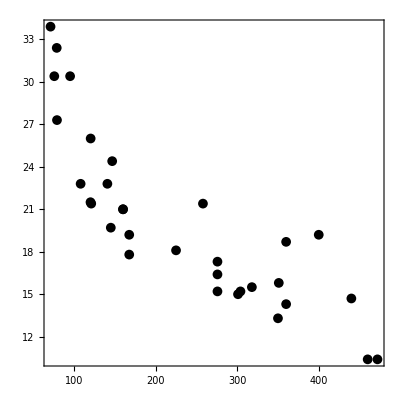

```mathematica
Graphics[graphicsPrimitives,Frame->True,AspectRatio->1]
```

```mathematica
Names["Charting`*Ticks*"]
```

{Charting`CategoricalTicksFunction,Charting`ComputeScaledTicks,Charting`convertTicks,Charting`DateTicksFunction,Charting`EvaluateTicksFunction,Charting`FindLogTicks,Charting`FindScaledTicks,Charting`FindTicks,Charting`FindTicksP,Charting`getDateTicks,Charting`PeriodicFrameTicks,Charting`PeriodicTicks,Charting`RotateTicks,Charting`SafeTicksFunctionQ,Charting`ScaledFrameTicks,Charting`ScaledTicks,Charting`ScaledTicks2,Charting`SimpleTicks,Charting`TicksFunction,Charting`unitTicksOnBar}

```mathematica
Names["Charting`*Date*"]
```

{Charting`adjustDateRange,Charting`DateAxis,Charting`DateDataParser,Charting`DateHeatmap,Charting`DatePlotParser,Charting`DateScale,Charting`DateScope,Charting`DateSpan,Charting`DateTicksFunction,Charting`DateValueParser,Charting`FindDateDivisions,Charting`fixDateGridLines,Charting`getDateTicks,Charting`iDateHeatmap,Charting`iDateHistogram,Charting`iDateListPlot,Charting`nearestDate}

```mathematica
Charting`FindDateDivisions[{Now,Now+Quantity[5,"Days"]},10]
Charting`FindDateDivisions[{AbsoluteTime@Now,AbsoluteTime[Now+Quantity[5,"Days"]]},10]
```

{{3.79719×10^9,Apr 30},{3.79728×10^9,May 01},{3.79737×10^9,May 02},{3.79745×10^9,May 03},{3.79754×10^9,May 04},{3.79763×10^9,May 05},{3.79771×10^9,May 06}}

{{3.79719×10^9,Apr 30},{3.79728×10^9,May 01},{3.79737×10^9,May 02},{3.79745×10^9,May 03},{3.79754×10^9,May 04},{3.79763×10^9,May 05},{3.79771×10^9,May 06}}

```mathematica
Charting`DateTicksFunction[{Now,Now+Quantity[5,"Days"]}]
```

Charting`DateTicksFunction[{Wed 29 Apr 2020 20:57:07GMT-5.,Mon 4 May 2020 20:57:07GMT-5.},DateTicksFormat→{Automatic}]

```mathematica
Charting`DateTicksFunction[{DateObject@Now,DateObject[Now+Quantity[5,"Days"]]},10]
```

Charting`DateTicksFunction[{Thu 30 Apr 2020 07:11:29GMT-5.,Tue 5 May 2020 07:11:29GMT-5.},10]

```mathematica
Options[Charting`DateTicksFunction]
```

{Alignment→Center,DateTicksFormat→Automatic,Exclusions→None,LabelingFunction→Automatic,Charting`LabelSide→Automatic,LabelStyle→{},Method→Automatic,Charting`PadLabels→Automatic,RotateLabel→Automatic,SaveDefinitions→False,ScalingFunctions→None,Charting`TickAnnotations→None,Charting`TickLabels→Automatic,Charting`TickLengths→Automatic,Charting`TickLevels→None,Charting`TickSide→Automatic,Ticks→None,TicksStyle→{},Charting`TickTemplate→None,Charting`TickWrappers→None}

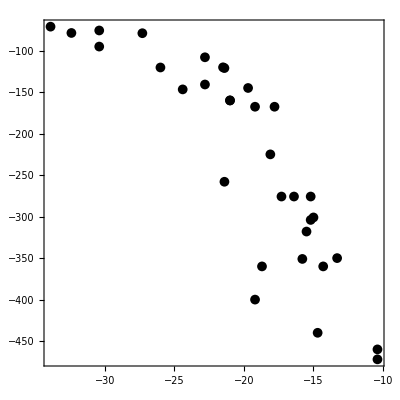

```mathematica
Graphics[GeometricTransformation[{Red,graphicsPrimitives},ReflectionTransform[{-1,-1}]],Frame->True,AspectRatio->1]
```

```mathematica
AffineTransform
```

```mathematica
mm=x//Transpose//Map[MinMax]
```

{{29.3241,995.013},{13.6287,977.428}}

```mathematica
x
```

{{891.065,236.666},{129.443,249.304},{753.784,589.46},{422.576,99.313},{390.227,343.934},{761.803,672.929},{412.919,685.539},{446.171,580.031},{662.715,438.062},{149.006,13.6287},{942.873,349.81},{345.488,74.7991},{724.946,685.394},{415.999,186.881},{773.869,806.993},{259.358,977.428},{122.164,191.762},{165.656,350.598},{266.201,861.733},{429.951,845.209},{76.8374,586.739},{297.405,797.065},{651.7,255.235},{372.917,747.532},{447.077,169.009},{947.698,602.575},{543.13,610.535},{995.013,803.896},{161.204,634.796},{35.8477,728.94},{900.601,45.0862},{590.924,289.473},{917.634,52.8401},{497.155,59.1239},{647.458,66.6291},{947.831,129.301},{944.796,945.299},{251.773,366.042},{957.772,52.019},{438.135,131.635},{442.838,471.548},{540.562,106.746},{29.3241,226.193},{504.522,254.124},{245.113,951.082},{463.581,260.814},{181.874,222.688},{550.566,441.65},{698.047,591.732},{208.279,432.103}}

```mathematica
blah=Flatten[{{{160,21}},{{160,21}},{{108,22.8}},{{258,21.4}},{{360,18.7}},{{225,18.1}},{{360,14.3}},{{146.7,24.4}},{{140.8,22.8}},{{167.6,19.2}},{{167.6,17.8}},{{275.8,16.4}},{{275.8,17.3}},{{275.8,15.2}},{{472,10.4}},{{460,10.4}},{{440,14.7}},{{78.7,32.4}},{{75.7,30.4}},{{71.1,33.9}},{{120.1,21.5}},{{318,15.5}},{{304,15.2}},{{350,13.3}},{{400,19.2}},{{79,27.3}},{{120.3,26}},{{95.1,30.4}},{{351,15.8}},{{145,19.7}},{{301,15}},{{121,21.4}}},1];
```

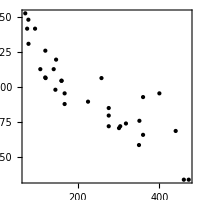

```mathematica
Graphics[Point@MapAt[Log,blah,{All,2}],Frame->True,ImageSize->200,AspectRatio->1]
```

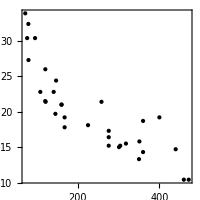

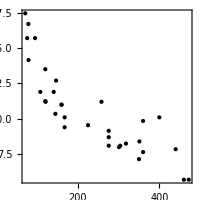

```mathematica
Graphics[Point@blah,Frame->True,ImageSize->200,AspectRatio->1]
Graphics[GeometricTransformation[Point@blah,RescalingTransform[{{-1,1},{-1,1}},{{-1,1},{0,1}}]],Frame->True,ImageSize->200,AspectRatio->1]
```

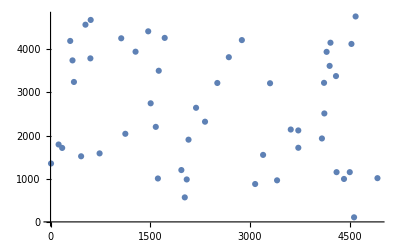

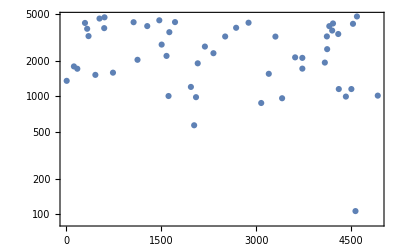

```mathematica
ListPlot[x]
ListPlot[x,ScalingFunctions->"Log",Frame->True]
```

```mathematica
ticks=Charting`ScaledTicks[{Log, Exp}][1,100,{6,6}]
```

{{2.30259,10,{0.01,0.}},{25.3284,10^11,{0.01,0.}},{48.3543,10^21,{0.01,0.}},{71.3801,10^31,{0.01,0.}},{94.406,10^41,{0.01,0.}},{6.90776,,{0.005,0.}},{11.5129,,{0.005,0.}},{16.1181,,{0.005,0.}},{20.7233,,{0.005,0.}},{29.9336,,{0.005,0.}},{34.5388,,{0.005,0.}},{39.1439,,{0.005,0.}},{43.7491,,{0.005,0.}},{52.9595,,{0.005,0.}},{57.5646,,{0.005,0.}},{62.1698,,{0.005,0.}},{66.775,,{0.005,0.}},{75.9853,,{0.005,0.}},{80.5905,,{0.005,0.}},{85.1956,,{0.005,0.}},{89.8008,,{0.005,0.}},{99.0112,,{0.005,0.}}}

```mathematica
Charting`ScaledTicks[{Log,Exp}][Log[1^2],Log[10^2],{6,6}]
```

{{0.,1,{0.01,0.}},{1.60944,5,{0.01,0.}},{2.30259,10,{0.01,0.}},{3.91202,50,{0.01,0.}},{4.60517,100,{0.01,0.}},{-0.693147,,{0.005,0.}},{-0.510826,,{0.005,0.}},{-0.356675,,{0.005,0.}},{-0.223144,,{0.005,0.}},{-0.105361,,{0.005,0.}},{0.693147,,{0.005,0.}},{1.09861,,{0.005,0.}},{1.38629,,{0.005,0.}},{1.79176,,{0.005,0.}},{1.94591,,{0.005,0.}},{2.07944,,{0.005,0.}},{2.19722,,{0.005,0.}},{2.99573,,{0.005,0.}},{3.4012,,{0.005,0.}},{3.68888,,{0.005,0.}},{4.09434,,{0.005,0.}},{4.2485,,{0.005,0.}},{4.38203,,{0.005,0.}},{4.49981,,{0.005,0.}},{5.29832,,{0.005,0.}},{5.70378,,{0.005,0.}},{5.99146,,{0.005,0.}},{6.21461,,{0.005,0.}},{6.39693,,{0.005,0.}},{6.55108,,{0.005,0.}},{6.68461,,{0.005,0.}},{6.80239,,{0.005,0.}},{6.90776,,{0.005,0.}}}

```mathematica
Charting`ScaledTicks["Log"][Log[1^2],Log[10^2],{6,6}]
```

{{0.,1,{0.01,0.}},{1.60944,5,{0.01,0.}},{2.30259,10,{0.01,0.}},{3.91202,50,{0.01,0.}},{4.60517,100,{0.01,0.}},{-0.693147,,{0.005,0.}},{-0.510826,,{0.005,0.}},{-0.356675,,{0.005,0.}},{-0.223144,,{0.005,0.}},{-0.105361,,{0.005,0.}},{0.693147,,{0.005,0.}},{1.09861,,{0.005,0.}},{1.38629,,{0.005,0.}},{1.79176,,{0.005,0.}},{1.94591,,{0.005,0.}},{2.07944,,{0.005,0.}},{2.19722,,{0.005,0.}},{2.99573,,{0.005,0.}},{3.4012,,{0.005,0.}},{3.68888,,{0.005,0.}},{4.09434,,{0.005,0.}},{4.2485,,{0.005,0.}},{4.38203,,{0.005,0.}},{4.49981,,{0.005,0.}},{5.29832,,{0.005,0.}},{5.70378,,{0.005,0.}},{5.99146,,{0.005,0.}},{6.21461,,{0.005,0.}},{6.39693,,{0.005,0.}},{6.55108,,{0.005,0.}},{6.68461,,{0.005,0.}},{6.80239,,{0.005,0.}},{6.90776,,{0.005,0.}}}

```mathematica
Charting`ScaledTicks["Identity"][1^2,10^2,{6,6}]
Charting`ScaledTicks["Linear"][1^2,10^2,{6,6}]
```

{{20.,20,{0.01,0.}},{40.,40,{0.01,0.}},{60.,60,{0.01,0.}},{80.,80,{0.01,0.}},{100.,100,{0.01,0.}},{0.,,{0.005,0.}},{5.,,{0.005,0.}},{10.,,{0.005,0.}},{15.,,{0.005,0.}},{25.,,{0.005,0.}},{30.,,{0.005,0.}},{35.,,{0.005,0.}},{45.,,{0.005,0.}},{50.,,{0.005,0.}},{55.,,{0.005,0.}},{65.,,{0.005,0.}},{70.,,{0.005,0.}},{75.,,{0.005,0.}},{85.,,{0.005,0.}},{90.,,{0.005,0.}},{95.,,{0.005,0.}}}

{{20.,20,{0.01,0.}},{40.,40,{0.01,0.}},{60.,60,{0.01,0.}},{80.,80,{0.01,0.}},{100.,100,{0.01,0.}},{0.,,{0.005,0.}},{5.,,{0.005,0.}},{10.,,{0.005,0.}},{15.,,{0.005,0.}},{25.,,{0.005,0.}},{30.,,{0.005,0.}},{35.,,{0.005,0.}},{45.,,{0.005,0.}},{50.,,{0.005,0.}},{55.,,{0.005,0.}},{65.,,{0.005,0.}},{70.,,{0.005,0.}},{75.,,{0.005,0.}},{85.,,{0.005,0.}},{90.,,{0.005,0.}},{95.,,{0.005,0.}}}

```mathematica
Charting`ScaledTicks["Reciprocal"][1^2,10^2,{6,6}]
```

{{100.,0.01,{0.01,0.}},{20.,0.05,{0.01,0.}},{1.,1,{0.01,0.}},{-10.,,{0.005,0.}},{-11.1111,,{0.005,0.}},{-12.5,,{0.005,0.}},{-14.2857,,{0.005,0.}},{-16.6667,,{0.005,0.}},{-20.,,{0.005,0.}},{-25.,,{0.005,0.}},{-33.3333,,{0.005,0.}},{-50.,,{0.005,0.}},{-100.,,{0.005,0.}},{50.,,{0.005,0.}},{33.3333,,{0.005,0.}},{25.,,{0.005,0.}},{10.,,{0.005,0.}}}

```mathematica
linearTicks[0,1]
```

{{0,0.0,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1/5,0.2,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{2/5,0.4,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{3/5,0.6,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{4/5,0.8,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1,1.0,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{2/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{3/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{4/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{6/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{7/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{8/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{9/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{11/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{12/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{13/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{14/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{16/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{17/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{18/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{19/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{21/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{22/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{23/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{24/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]}}

```mathematica
Options[linearTicks]
```

{numberOfMajorTicks→8,numberOfMinorTicksPerMajorTick→5,tickStyle→Directive[GrayLevel[0],Thickness[0.001]],majorTickLength→{0.,0.},minorTickLength→{0.,0.},tickLabelFunction→Automatic,extraMajorTicks→{}}

```mathematica
Remove[ticks];
Options[ticks]={numberOfMajorTicks->8,numberOfMinorTicksPerMajorTick->5,tickStyle->Directive[GrayLevel[0],Thickness[0.001]],majorTickLength->{0.,0.},minorTickLength->{0.,0.},tickLabelFunction->Automatic,extraMajorTicks->{}};
ticks[list_?ListQ,opts:OptionsPattern[]]:=ReplaceAll[list,{
	(*Major ticks*)
	{value_,display:(_?NumericQ|_NumberForm),tickDistance_}:>{value,display,OptionValue[majorTickLength],OptionValue[tickStyle]},
	(*Minor ticks*)
	{value_,display:(_?StringQ|_Spacer),tickDistance_}:>{value,display,OptionValue[minorTickLength],OptionValue[tickStyle]}
}];
ticks[min_?NumericQ,max_?NumericQ,opts:OptionsPattern[]]:=ticks[Charting`ScaledTicks["Identity"][min,max,{OptionValue[numberOfMajorTicks],OptionValue[numberOfMinorTicksPerMajorTick]}],opts];
ticks[func_?StringQ,min_?NumericQ,max_?NumericQ,opts:OptionsPattern[]]:=ticks[Charting`ScaledTicks[func][min,max,{OptionValue[numberOfMajorTicks],OptionValue[numberOfMinorTicksPerMajorTick]}],opts]
```

```mathematica
ticks[0,1]
```

{{0.,0,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.2,0.2,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.4,0.4,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.6,0.6,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.8,0.8,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1.,1.0,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.05,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.1,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.15,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.3,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.35,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.45,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.5,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.55,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.65,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.7,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.75,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.85,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.9,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.95,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]}}

```mathematica
ticks["Identity",0,1]
```

{{0.,0,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.2,0.2,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.4,0.4,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.6,0.6,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.8,0.8,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1.,1.0,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.05,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.1,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.15,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.3,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.35,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.45,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.5,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.55,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.65,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.7,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.75,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.85,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.9,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.95,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]}}

```mathematica
ticks["Log",Log@2,Log@100]
```

{{1.60944,5,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{2.30259,10,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{3.91202,50,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{4.60517,100,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.693147,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1.09861,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1.38629,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1.79176,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1.94591,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{2.07944,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{2.19722,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{2.99573,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{3.4012,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{3.68888,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{4.09434,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{4.2485,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{4.38203,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{4.49981,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{5.29832,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{5.70378,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{5.99146,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{6.21461,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]}}

```mathematica
x=Table[{x,x^2},{x,1,10}]
```

{{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}}

```mathematica
ticks[1,100]
ticks["Log",Log@1,Log@100]
ticks["Log2",Log@1,Log@100]
```

{{20.,20,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{40.,40,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{60.,60,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{80.,80,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{100.,100,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{5.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{10.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{15.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{25.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{30.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{35.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{45.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{50.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{55.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{65.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{70.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{75.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{85.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{90.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{95.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]}}

{{0.,1,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1.60944,5,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{2.30259,10,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{3.91202,50,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{4.60517,100,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{-0.693147,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{-0.510826,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{-0.356675,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{-0.223144,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{-0.105361,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.693147,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1.09861,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1.38629,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1.79176,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1.94591,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{2.07944,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{2.19722,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{2.99573,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{3.4012,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{3.68888,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{4.09434,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{4.2485,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{4.38203,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{4.49981,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{5.29832,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{5.70378,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{5.99146,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{6.21461,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{6.39693,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{6.55108,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{6.68461,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{6.80239,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{6.90776,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]}}

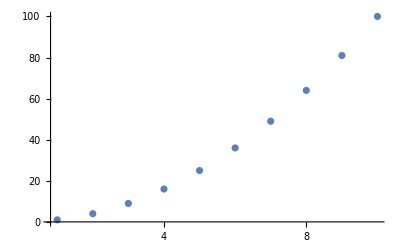

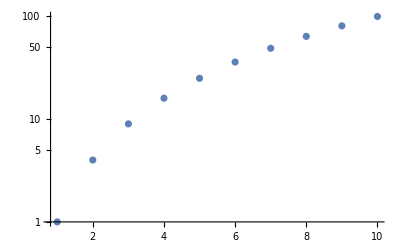

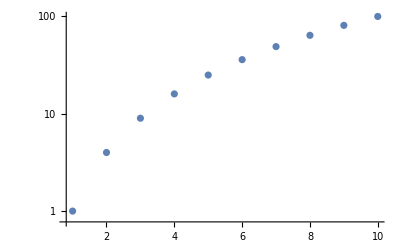

```mathematica
ListPlot[x,Ticks->{ticks[0,10],ticks[0,100]}]
ListPlot[x//MapAt[Log,{All,2}],Ticks->{ticks[#1,#2]&,ticks["Log",#1,#2]&}]
ListPlot[x,ScalingFunctions->{None,"Log"}]
```

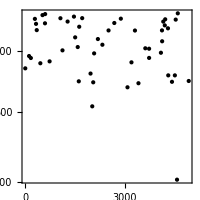

```mathematica
x//MapAt[Log,{All,2}]//
	Point//
	op[Graphics[Frame->True,ImageSize->200,AspectRatio->1,FrameTicks->{{Charting`ScaledTicks["Log"](*Function[Charting`ScaledTicks[{Log, Exp}][#, #2, {6, 6}]]*),None},{Automatic,None}}]]
```

```mathematica
Names["*Transform*"]//TableForm
```

AffineTransform
AudioSpectralTransformation
BottomHatTransform
ConfidenceTransform
ContinuousWaveletTransform
CoordinateTransform
CoordinateTransformData
DirichletTransform
DiscreteChirpZTransform
DiscreteHadamardTransform
DiscreteWaveletPacketTransform
DiscreteWaveletTransform
DistanceTransform
FillingTransform
FindGeometricTransform
FourierCosTransform
FourierSequenceTransform
FourierSinTransform
FourierTransform
GeometricTransformation
GeometricTransformation3DBox
GeometricTransformation3DBoxOptions
GeometricTransformationBox
GeometricTransformationBoxOptions
HankelTransform
HistogramTransform
HistogramTransformInterpolation
HitMissTransform
ImageForwardTransformation
ImagePerspectiveTransformation
ImageTransformation
InverseContinuousWaveletTransform
InverseDistanceTransform
InverseFourierCosTransform
InverseFourierSequenceTransform
InverseFourierSinTransform
InverseFourierTransform
InverseHankelTransform
InverseLaplaceTransform
InverseMellinTransform
InverseRadonTransform
InverseTransformedRegion
InverseWaveletTransform
InverseZTransform
LaplaceTransform
LiftingWaveletTransform
LinearFractionalTransform
LinearizingTransformationData
ListFourierSequenceTransform
ListZTransform
MellinTransform
MorphologicalTransform
NondimensionalizationTransform
RadonTransform
ReflectionTransform
RescalingTransform
RotationTransform
ScalingTransform
ShearingTransform
SkeletonTransform
SpatialTransformationLayer
StateSpaceTransform
StateTransformationLinearize
StationaryWaveletPacketTransform
StationaryWaveletTransform
TopHatTransform
TransferFunctionTransform
TransformationClass
TransformationFunction
TransformationFunctions
TransformationMatrix
TransformedDistribution
TransformedField
TransformedProcess
TransformedRegion
TranslationTransform
ZTransform

```mathematica
ImageForwardTransformation
```